## Handling Excel Data

### Functions

node: {identifier, degree, cluster,{x,y,z},r}

```mathematica
restoreCoords:=Function[{rawJunctions},
	restoredJunctions=rawJunctions;
	restoredJunctions⟦;;,1⟧=StringReplace[rawJunctions⟦;;,1⟧,{"C"->"0","D"->"1","E"->"2","F"->"3","G"->"4"}];
	restoredJunctions⟦;;,1⟧=ToExpression[restoredJunctions⟦;;,1⟧];
	restoredJunctions⟦;;,1⟧=Mod[restoredJunctions⟦;;,1⟧,12000]-21;
	baseX=IntegerPart[restoredJunctions⟦;;,1⟧/100];
	baseY=IntegerPart[Mod[restoredJunctions⟦;;,1⟧,100]/10];
	baseZ=Mod[restoredJunctions⟦;;,1⟧,10];
	x=baseX*40+restoredJunctions⟦;;,2⟧;
	y=baseY*40+restoredJunctions⟦;;,3⟧;
	z=baseZ*40+restoredJunctions⟦;;,4⟧;
	trueBallsTable = Table[{i,restoredJunctions⟦i,5⟧,{{i,{x⟦i⟧,y⟦i⟧,z⟦i⟧},restoredJunctions⟦i,6⟧}},{x⟦i⟧,y⟦i⟧,z⟦i⟧},restoredJunctions⟦i,6⟧},{i,Length[restoredJunctions]}];
	{trueBallsTable,restoredJunctions}
]
```

### Ground truth data processing

```mathematica
Clear["Global`*"];
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"]⟦1,2;;⟧;
rawJunctions = groundTruthTable[[;;,{3,4,5,6,10,19}]];
{trueBallsTable,restoredJunctions}=restoreCoords[rawJunctions];
```

Set::shape: Lists {trueBallsTable,restoredJunctions} and restoreCoords[{{12C22,45.,45.,47.,3.,7.},{12C23,30.,7.,50.,3.,7.56058},{12C33,10.,38.,40.,3.,3.24911},{12C33,37.,45.,35.,4.,7.},«44»,{12D52,21.,30.,5.,3.,4.38013},{12D53,50.,15.,50.,4.,4.86644},«115»}] are not the same shape.

```mathematica
unitCubes=Table[Cuboid[{(i-1)*40,(j-1)*40,(k-1)*40},{40,40,40}],{i,6},{j,6},{k,6}];
Dimensions[unitCubes]
```

{6,6,6}

```mathematica
trueJunctionBalls=Table[{Ball[trueBallsTable⟦i,4⟧,trueBallsTable⟦i,5⟧]},{i,Dimensions[trueBallsTable]⟦1⟧}];
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {i,{}⟦1⟧} does not have appropriate bounds.

```mathematica
trueJunctionBalls
```

{{Ball[{45.,45.,87.},7.]},{Ball[{30.,7.,130.},7.56058]},{Ball[{10.,78.,120.},3.24911]},{Ball[{37.,85.,115.},7.]},{Ball[{40.,60.,165.},8.51508]},{Ball[{20.,75.,170.},12.4307]},{Ball[{5.,45.,205.},4.93311]},{Ball[{40.,80.,130.},11.1118]},{Ball[{35.,87.,100.},10.0957]},{Ball[{27.,107.,101.},4.93311]},{Ball[{30.,110.,165.},7.]},{Ball[{10.,155.,55.},6.21533]},{Ball[{5.,162.,85.},9.2933]},{Ball[{43.,127.,110.},6.49822]},{Ball[{35.,150.,105.},3.91541]},{Ball[{9.,159.,112.},8.51508]},{Ball[{10.,167.,122.},7.]},{Ball[{5.,125.,207.},7.]},{Ball[{10.,145.,185.},8.35438]},{Ball[{30.,140.,195.},6.21533]},{Ball[{47.,132.,172.},5.5559]},{Ball[{19.,150.,179.},5.48081]},{Ball[{9.,159.,192.},7.]},{Ball[{30.,155.,201.},7.83082]},{Ball[{20.,190.,168.},3.24911]},{Ball[{50.,47.,99.},7.22596]},{Ball[{76.,50.,109.},3.3742]},{Ball[{75.,60.,109.},3.33354]},{Ball[{74.,68.,106.},3.86249]},{Ball[{61.,75.,121.},11.5567]},{Ball[{60.,87.,130.},5.51861]},{Ball[{75.,53.,168.},2.48983]},{Ball[{56.,118.,50.},7.22596]},{Ball[{47.,127.,76.},3.63475]},{Ball[{81.,110.,75.},8.81945]},{Ball[{40.,120.,100.},11.1579]},{Ball[{55.,95.,102.},5.15764]},{Ball[{43.,86.,105.},3.7193]},{Ball[{71.,105.,100.},2.64583]},{Ball[{65.,102.,127.},5.36417]},{Ball[{45.,85.,145.},7.1819]},{Ball[{75.,127.,153.},5.5559]},{Ball[{50.,112.,125.},7.67873]},{Ball[{75.,86.,179.},9.34596]},{Ball[{52.,120.,190.},10.7283]},{Ball[{68.,108.,190.},3.24911]},{Ball[{47.,135.,55.},7.63975]},{Ball[{68.,135.,44.},7.83082]},{Ball[{61.,150.,45.},4.38013]},{Ball[{90.,135.,130.},4.86644]},{Ball[{61.,168.,118.},3.24911]},{Ball[{51.,163.,126.},7.43861]},{Ball[{63.,122.,128.},3.91541]},{Ball[{56.,165.,165.},8.78995]},{Ball[{67.,153.,155.},5.24221]},{Ball[{72.,137.,140.},7.]},{Ball[{45.,126.,166.},8.33797]},{Ball[{42.,175.,97.},2.74041]},{Ball[{40.,200.,95.},5.5927]},{Ball[{81.,200.,130.},5.70028]},{Ball[{47.,185.,135.},15.3283]},{Ball[{87.,166.,190.},3.86249]},{Ball[{83.,170.,209.},6.94117]},{Ball[{95.,88.,20.},4.86644]},{Ball[{116.,73.,28.},4.97965]},{Ball[{129.,72.,28.},5.5559]},{Ball[{114.,61.,37.},3.91541]},{Ball[{106.,79.,46.},3.01621]},{Ball[{119.,61.,53.},5.90403]},{Ball[{110.,65.,75.},16.3103]},{Ball[{90.,45.,95.},6.03242]},{Ball[{105.,55.,138.},12.4307]},{Ball[{115.,63.,158.},3.4527]},{Ball[{120.,70.,170.},8.70025]},{Ball[{119.,89.,166.},3.66904]},{Ball[{89.,98.,38.},5.90403]},{Ball[{82.,117.,17.},4.38013]},{Ball[{99.,95.,49.},4.86644]},{Ball[{121.,108.,3.},6.35992]},{Ball[{98.,87.,60.},9.52573]},{Ball[{105.,90.,49.},6.75843]},{Ball[{102.,118.,150.},5.7698]},{Ball[{86.,109.,130.},4.40972]},{Ball[{99.,117.,134.},4.6227]},{Ball[{102.,119.,150.},7.28029]},{Ball[{105.,102.,120.},3.5]},{Ball[{125.,115.,153.},7.]},{Ball[{126.,110.,145.},5.15764]},{Ball[{90.,145.,6.},6.75843]},{Ball[{99.,135.,25.},4.06615]},{Ball[{115.,150.,20.},8.74533]},{Ball[{109.,155.,12.},6.27397]},{Ball[{97.,142.,62.},4.42145]},{Ball[{107.,135.,60.},4.38013]},{Ball[{102.,145.,80.},5.90403]},{Ball[{120.,130.,80.},13.2618]},{Ball[{123.,142.,46.},5.48081]},{Ball[{98.,142.,120.},5.90403]},{Ball[{101.,168.,105.},7.83082]},{Ball[{105.,127.,130.},8.32149]},{Ball[{128.,128.,165.},3.7193]},{Ball[{80.,145.,168.},7.83082]},{Ball[{92.,172.,65.},9.86622]},{Ball[{110.,200.,72.},10.7283]},{Ball[{115.,165.,96.},7.]},{Ball[{115.,172.,102.},4.68603]},{Ball[{117.,173.,102.},4.6227]},{Ball[{125.,195.,110.},6.09461]},{Ball[{91.,163.,95.},6.49822]},{Ball[{87.,202.,115.},11.0184]},{Ball[{85.,185.,130.},7.]},{Ball[{87.,207.,127.},3.95235]},{Ball[{105.,163.,147.},4.16075]},{Ball[{108.,163.,168.},4.16075]},{Ball[{105.,190.,145.},6.66708]},{Ball[{89.,196.,165.},5.70028]},{Ball[{88.,198.,148.},7.43861]},{Ball[{153.,60.,7.},5.7698]},{Ball[{147.,89.,19.},6.49822]},{Ball[{161.,55.,70.},9.62548]},{Ball[{161.,77.,48.},6.75843]},{Ball[{160.,80.,123.},9.15899]},{Ball[{150.,42.,144.},5.70028]},{Ball[{150.,59.,125.},9.04304]},{Ball[{153.,117.,23.},10.2613]},{Ball[{147.,93.,43.},3.2052]},{Ball[{130.,80.,70.},3.01621]},{Ball[{167.,100.,48.},5.15764]},{Ball[{141.,120.,125.},8.51508]},{Ball[{130.,100.,140.},3.95235]},{Ball[{145.,110.,125.},6.75843]},{Ball[{131.,112.,150.},3.13698]},{Ball[{123.,120.,140.},4.09362]},{Ball[{156.,120.,166.},4.57949]},{Ball[{135.,135.,17.},8.62406]},{Ball[{150.,153.,15.},6.21533]},{Ball[{122.,142.,50.},6.21533]},{Ball[{160.,125.,47.},6.06367]},{Ball[{131.,132.,70.},8.32149]},{Ball[{164.,132.,63.},4.42145]},{Ball[{170.,151.,69.},4.57949]},{Ball[{150.,130.,70.},5.15764]},{Ball[{145.,157.,82.},8.51508]},{Ball[{135.,122.,100.},7.]},{Ball[{145.,130.,90.},6.75843]},{Ball[{133.,145.,105.},9.74734]},{Ball[{123.,164.,110.},3.4527]},{Ball[{153.,165.,118.},5.15764]},{Ball[{157.,150.,170.},3.91541]},{Ball[{142.,136.,155.},7.43861]},{Ball[{141.,150.,135.},8.22122]},{Ball[{152.,166.,67.},3.91541]},{Ball[{125.,201.,47.},4.68603]},{Ball[{165.,192.,61.},4.68603]},{Ball[{155.,205.,69.},7.]},{Ball[{144.,165.,83.},6.92452]},{Ball[{150.,179.,89.},3.24911]},{Ball[{160.,195.,82.},2.54397]},{Ball[{125.,197.,95.},6.27397]},{Ball[{132.,200.,93.},4.38013]},{Ball[{145.,186.,125.},6.21533]},{Ball[{151.,193.,132.},3.4527]},{Ball[{155.,185.,135.},7.83827]},{Ball[{129.,207.,141.},5.8644]},{Ball[{185.,88.,132.},4.86644]}}

```mathematica
points1=coordsAlign[points1,trueBallsTable⟦;;,4⟧];
skelCube1=Table[{Green,Thickness[0.004],Line[{points1⟦skelLine⟦1⟧⟧,points1⟦skelLine⟦2⟧⟧}]},{skelLine,lines1}];
Show[Graphics3D[{skelCube1,{Opacity[0.5],Blue,trueJunctionBalls}}]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of coordsAlign[points1,Symbol[]].

Table::iterb: Iterator {skelLine,lines1} does not have appropriate bounds.

-Graphics3D-

```mathematica
points2=coordsAlign[points2,trueBallsTable⟦;;,4⟧];
skelCube2=Table[{Green,Thickness[0.004],Line[{points2⟦skelLine⟦1⟧⟧,points2⟦skelLine⟦2⟧⟧}]},{skelLine,lines2}];
Show[Graphics3D[{skelCube2,{Opacity[0.5],Blue,trueJunctionBalls}}]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of coordsAlign[points2,Symbol[]].

Table::iterb: Iterator {skelLine,lines2} does not have appropriate bounds.

-Graphics3D-

```mathematica
points3=coordsAlign[points3,trueBallsTable⟦;;,4⟧];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of coordsAlign[points3,Symbol[]].

```mathematica
skelCube3=Table[{Green,Thickness[0.004],Line[{points3⟦skelLine⟦1⟧⟧,points3⟦skelLine⟦2⟧⟧}]},{skelLine,lines3}];
Show[Graphics3D[{skelCube3,{Opacity[0.5],Blue,trueJunctionBalls}}]]
```

Table::iterb: Iterator {skelLine,lines3} does not have appropriate bounds.

-Graphics3D-

```mathematica
points4=coordsAlign[points4,trueBallsTable⟦;;,4⟧];
skelCube4=Table[{Green,Thickness[0.004],Line[{points4⟦skelLine⟦1⟧⟧,points4⟦skelLine⟦2⟧⟧}]},{skelLine,lines4}];
Show[Graphics3D[{skelCube4,{Opacity[0.5],Blue,trueJunctionBalls}}]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of coordsAlign[points4,Symbol[]].

Table::iterb: Iterator {skelLine,lines4} does not have appropriate bounds.

-Graphics3D-

## Visualization

```mathematica
theEdgeInCoords = Table[{Green,Thickness[0.003],Line[{thepoints⟦skelLine⟦1⟧⟧,thepoints⟦skelLine⟦2⟧⟧}]},{skelLine,thelines}];
```

```mathematica
theBasicBalls=Table[{Opacity[0.5], degreeColor[theJ⟦i, 2⟧], Ball[theJ⟦i,4⟧,theJ⟦i,5⟧]},{i,Dimensions[theJ]⟦1⟧}];
```

```mathematica
theMergedBalls=Table[{Opacity[0.5], degreeColor[theJres⟦i, 2⟧], Ball[theJres⟦i,4⟧,theJres⟦i,5⟧]},{i,Dimensions[theJres]⟦1⟧}];
```

```mathematica
Manipulate[
	Show[Graphics3D[{
			If[showEdges,theEdgeInCoords],
			If[showBasicBalls,theBasicBalls],
			If[showMergedBalls,theMergedBalls]
		}]
	],
	{showEdges, {True, False}},
	{showBasicBalls, {True, False}},
	{showMergedBalls, {True, False}}
]
```

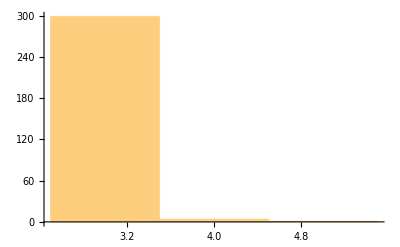

```mathematica
Histogram[theJ⟦;;,2⟧]
```

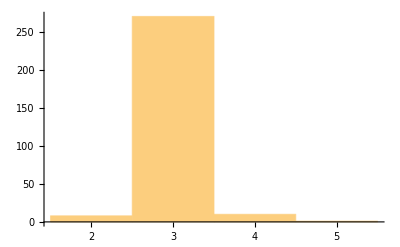

```mathematica
Histogram[theJres⟦;;,2⟧]
```